```mathematica
(*Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]*)
```

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
(*IGDocumentation[]*)
```

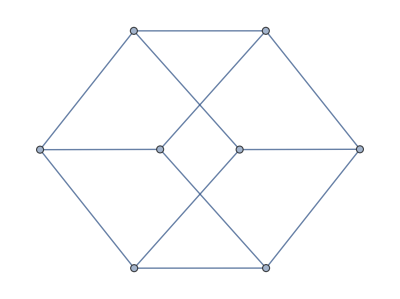

```mathematica
cGraph=Graph[{i<->j,i<->k,j<->l,k<->l,ip<->jp,ip<->kp,jp<->lp,kp<->lp,i<->ip,j<->jp,k<->kp,l<->lp}]
```

```mathematica
VertexList@cGraph
```

{i,j,k,l,ip,jp,kp,lp}

```mathematica
ChordLessCycles[graph_]:=
Select[
FindCycle[graph,∞,All],
Module[
{cycleSubgraph=Subgraph[graph,VertexList@#]},
IGSameGraphQ[
cycleSubgraph,
Graph[FindFundamentalCycles[cycleSubgraph][[1]]]
]
]&
]
```

```mathematica
2+Length@EdgeList@cGraph-Length@VertexList@cGraph
```

6

```mathematica
AllTrue[
Tally[
Sort@{#[[1]],#[[2]]}&/@Flatten@#&@Subsets[ChordLessCycles[cGraph],{2+Length@EdgeList@cGraph-Length@VertexList@cGraph}][[1]]
][[All,2]],
#==2&
]
```

True

```mathematica
EdgeSortedPairsList[graphEdges_]:=Sort@{#[[1]],#[[2]]}&/@graphEdges
```

```mathematica
AllEdgeValences2Q[cycles_]:=
AllTrue[
Tally[
EdgeSortedPairsList@Flatten@cycles
][[All,2]],
#==2&
]
```

```mathematica
(*EdgeCompleteCyclesQ[graph_,cycles_]:=SubsetQ[Flatten[EdgeSortedPairsList@#&/@cycles,1],EdgeSortedPairsList@graph]*)
```

```mathematica
(*VertexCompleteCyclesQ[cycles_,graph_]:=SubsetQ[Flatten[EdgeSortedPairsList@#&/@cycles],VertexList@graph]*)
```

```mathematica
CompleteCyclesQ[graph_,cycles_]:=
Module[
{sortedEdgeList=Flatten[EdgeSortedPairsList@#&/@cycles,1]},
SubsetQ[sortedEdgeList,EdgeSortedPairsList@EdgeList@graph]&&SubsetQ[Flatten@sortedEdgeList,VertexList@graph]
]
```

```mathematica
SensicalIntersectionQ[cycle1_,cycle2_]:=Intersection[SortedVertexList@cycle1,SortedVertexList@cycle2]<=1
```

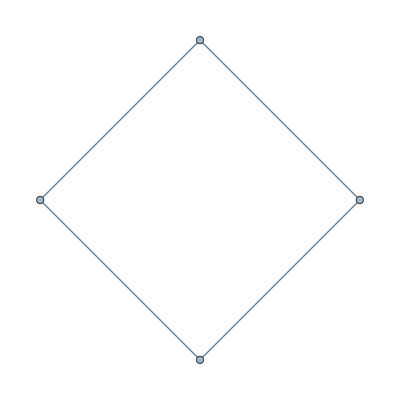
{1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{Length@#,Graph@#&/@#[[1]]}&@Select[
Select[
Subsets[ChordLessCycles[cGraph],{2+Length@EdgeList@cGraph-Length@VertexList@cGraph}],
CompleteCyclesQ[cGraph,#]&&AllEdgeValences2Q@#&
],
CompleteCyclesQ[cGraph,#]&
]
```

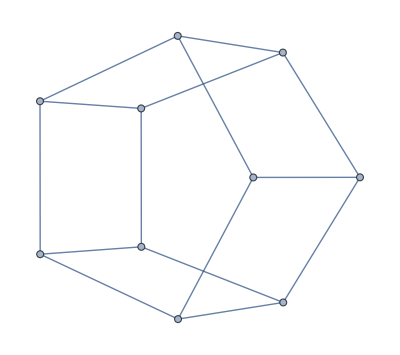

```mathematica
Graph@{v1<->v2,v2<->v3,v3<->v4,v4<->v5,v5<->v1,v1p<->v2p,v2p<->v3p,v3p<->v4p,v4p<->v5p,v5p<->v1p,v1<->v1p,v2<->v2p,v3<->v3p,v4<->v4p,v5<->v5p}
```

```mathematica
{Length@#,Graph@#&/@#[[1]]}&@Select[
Select[
Subsets[ChordLessCycles[pPGraph],{2+Length@EdgeList@pPGraph-Length@VertexList@pPGraph}],
CompleteCyclesQ[pPGraph,#]&&AllEdgeValences2Q@#&
],
CompleteCyclesQ[pPGraph,#]&
]
```

FindFundamentalCycles::graph: A graph object is expected at position 1 in FindFundamentalCycles[Subgraph[pPGraph,VertexList[pPGraph]]].

VertexList::graph: A graph object is expected at position 1 in VertexList[∞].

FindFundamentalCycles::graph: A graph object is expected at position 1 in FindFundamentalCycles[Subgraph[pPGraph,VertexList[∞]]].

FindFundamentalCycles::graph: A graph object is expected at position 1 in FindFundamentalCycles[Subgraph[pPGraph,VertexList[All]]].

General::stop: Further output of FindFundamentalCycles::graph will be suppressed during this calculation.

FindCycle::argb: FindCycle called with 0 arguments; between 1 and 3 arguments are expected.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression Graph[1] cannot be used as a part specification.

{0,(-Graphics-)⟦Graph[1]⟧}

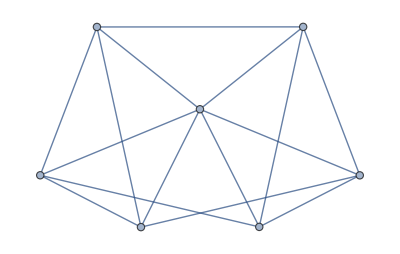

```mathematica
rGraph=Graph[{0<->i,0<->j,0<->k,0<->ip,0<->jp,0<->kp,i<->ip,j<->jp,k<->kp,i<->j,j<->k,k<->i,ip<->jp,jp<->kp,kp<->ip}]
```

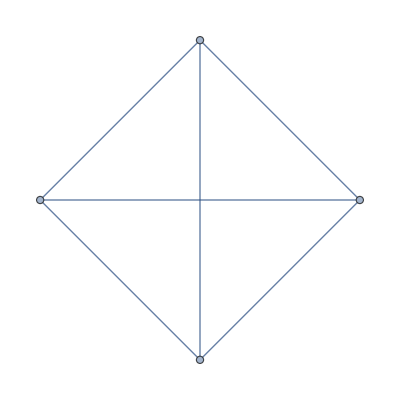
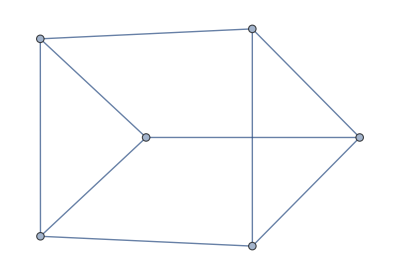
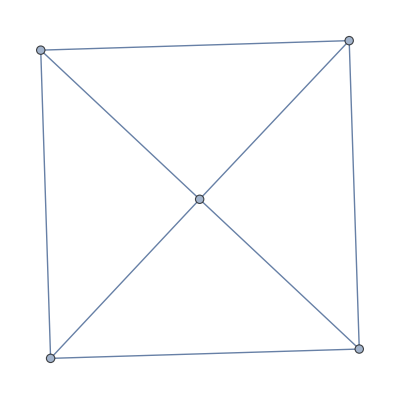
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Subgraph[rGraph,#]&/@{{0,i,j,k},{0,ip,jp,kp},{i,j,k,ip,jp,kp},{0,i,j,ip,jp},{0,j,k,jp,kp},{0,k,i,kp,ip}}
```

```mathematica
Select[
Table[
{
intersection,
CountsBy[
{{0,i,j,k},{0,ip,jp,kp},{i,j,k,ip,jp,kp},{0,i,j,ip,jp},{0,j,k,jp,kp},{0,k,i,kp,ip}},
SubsetQ[#,intersection]&
][True]
},
{intersection,Intersection@@@Subsets[{{0,i,j,k},{0,ip,jp,kp},{i,j,k,ip,jp,kp},{0,i,j,ip,jp},{0,j,k,jp,kp},{0,k,i,kp,ip}},{2}]
}
],
#[[2]]==2&
][[All,1]]
```

{{i,j,k},{0,i,j},{0,j,k},{0,i,k},{ip,jp,kp},{0,ip,jp},{0,jp,kp},{0,ip,kp},{i,ip,j,jp},{j,jp,k,kp},{i,ip,k,kp},{0,j,jp},{0,i,ip},{0,k,kp}}

```mathematica
CoDimTwoFaces[coFaces_]:=
Select[
Table[
{
intersection,
CountsBy[
coFaces,
SubsetQ[#,intersection]&
][True]
},
{intersection,Intersection@@@Subsets[coFaces,{2}]
}
],
#[[2]]==2&
][[All,1]]
```

```mathematica
CoFacesCodimTwoDecomposition[coFaces_]:=
Module[
{coDimTwoFaces=CoDimTwoFaces[coFaces]},
Table[
{
coFace,
Select[coDimTwoFaces,SubsetQ[coFace,#]&]
},
{coFace,coFaces}
]
]
```

```mathematica
FaceLattice[coFaces_,d_]:=
Module[
{lattice={CoFacesCodimTwoDecomposition[coFaces],{{DeleteDuplicates@Flatten@coFaces,coFaces}}}},
(*Print@lattice[[1]];*)
Do[
PrependTo[
lattice,
DeleteDuplicates@Flatten[CoFacesCodimTwoDecomposition[#]&/@lattice[[1,All,2]],1]
],
{d-2}
];
lattice=Append[DeleteDuplicates@Flatten[#[[All,2]],1]&/@lattice,{DeleteDuplicates@Flatten@coFaces}]
]
```

```mathematica
FaceLattice[{{0,i,j,k},{0,ip,jp,kp},{i,j,k,ip,jp,kp},{0,i,j,ip,jp},{0,j,k,jp,kp},{0,k,i,kp,ip}},4]
```

{{{j},{i},{k},{0},{jp},{ip},{kp}},{{i,j},{j,k},{i,k},{0,j},{0,i},{0,k},{ip,jp},{jp,kp},{ip,kp},{0,jp},{0,ip},{0,kp},{j,jp},{i,ip},{k,kp}},{{i,j,k},{0,i,j},{0,j,k},{0,i,k},{ip,jp,kp},{0,ip,jp},{0,jp,kp},{0,ip,kp},{i,ip,j,jp},{j,jp,k,kp},{i,ip,k,kp},{0,j,jp},{0,i,ip},{0,k,kp}},{{0,i,j,k},{0,ip,jp,kp},{i,j,k,ip,jp,kp},{0,i,j,ip,jp},{0,j,k,jp,kp},{0,k,i,kp,ip}},{{0,i,j,k,ip,jp,kp}}}